# Interacting Dark Energy with a Quadratic EoS with a Late-Time Cosmological Constant

## Manipulate Plots

#### Non-Compact x - z Phase Space

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→3/q,z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→ℛ,z→0},{x→(-1-wx)/ϵ,z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-3-3 wx-q z-6 x ϵ+3 ℛ ϵ | -q x
q z | -3+q x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(3/q
((-3+q ℛ) (q+q wx+3 ϵ))/q^2) | (-q (1+wx) ℛ-(9 ϵ)/q | -3
((-3+q ℛ) (q+q wx+3 ϵ))/q | 0) | ((-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)
(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)) | (-(q^2 ℛ+q^2 wx ℛ+9 ϵ+√(36 q^2+36 q^2 wx-12 q^3 ℛ-12 q^3 wx ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+108 q ϵ-18 q^2 ℛ ϵ+18 q^2 wx ℛ ϵ+81 ϵ^2))/(2 (-3+q ℛ) (q+q wx+3 ϵ)) | 1
-(q^2 ℛ+q^2 wx ℛ+9 ϵ-√(36 q^2+36 q^2 wx-12 q^3 ℛ-12 q^3 wx ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+108 q ϵ-18 q^2 ℛ ϵ+18 q^2 wx ℛ ϵ+81 ϵ^2))/(2 (-3+q ℛ) (q+q wx+3 ϵ)) | 1)
(ℛ
0) | (-3 (1+wx+ℛ ϵ) | -q ℛ
0 | -3+q ℛ) | (-3+q ℛ
-3 (1+wx+ℛ ϵ)) | (-(q ℛ)/(3 wx+q ℛ+3 ℛ ϵ) | 1
1 | 0)
((-1-wx)/ϵ
0) | (3 (1+wx+ℛ ϵ) | (q (1+wx))/ϵ
0 | -(q+q wx+3 ϵ)/ϵ) | ((-q-q wx-3 ϵ)/ϵ
3 (1+wx+ℛ ϵ)) | (-(q (1+wx))/(q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2) | 1
1 | 0)

```mathematica
(*Find the condition for spiral fixed point to be complex*)
wxCond=Solve[(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)==0,{ϵ,q,wx}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ϵ→1/9 (-6 q+q^2 ℛ-q^2 wx ℛ-2 √(-9 q^2 wx+6 q^3 wx ℛ-q^4 wx ℛ^2))},{ϵ→1/9 (-6 q+q^2 ℛ-q^2 wx ℛ+2 √(-9 q^2 wx+6 q^3 wx ℛ-q^4 wx ℛ^2))}}

```mathematica
(*Define the differential equations in terms of their parameters*)
DE[wx_,q_,ϵ_,ℛ_]=dex;
DM[q_]=dez;
```

```mathematica
(*Plot the phase space for the dark energy and the dark matter*)
Manipulate[StreamPlot[{DE[wx,q,ϵ,ℛ],DM[q]},{x,0,5},{z,0,3},FrameLabel->{"x","z"}],{q,0,20,Appearance->"Open"},{wx,-10,10,Appearance->"Open"},{ϵ,-2,2,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

#### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
de1:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→-x-3 wx x+3 ℛ+3 wx ℛ-3 x^2 ϵ+3 x ℛ ϵ},{x→3/q,y→-(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q),z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→3/q,y→(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q),z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→ℛ,y→-(√ℛ)/(√3),z→0},{x→ℛ,y→(√ℛ)/(√3),z→0},{x→(-1-wx)/ϵ,y→-(√(-1-wx))/(√3 √ϵ),z→0},{x→(-1-wx)/ϵ,y→(√(-1-wx))/(√3 √ϵ),z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
FP[7]={x/.FPs[[7,1]],y/.FPs[[7,2]],z/.FPs[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,7}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(-y (3+3 wx+q z+6 x ϵ-3 ℛ ϵ) | -q x z-3 (x-ℛ) (1+wx+x ϵ) | -q x y
1/6 (-1-3 wx-6 x ϵ+3 ℛ ϵ) | -2 y | -1/6
q y z | (-3+q x) z | (-3+q x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
-x-3 wx x+3 ℛ+3 wx ℛ-3 x^2 ϵ+3 x ℛ ϵ) | (0 | -3 (x-ℛ) (1+wx+x ϵ)+q x (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ)) | 0
1/6 (-1-3 wx-6 x ϵ+3 ℛ ϵ) | 0 | -1/6
0 | -((-3+q x) (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ))) | 0) | (0
-(√(wx x+3 wx^2 x-q wx x^2-3 q wx^2 x^2+2 ℛ-wx ℛ-3 wx^2 ℛ+3 q wx x ℛ+3 q wx^2 x ℛ+4 x^2 ϵ+9 wx x^2 ϵ-2 q x^3 ϵ-9 q wx x^3 ϵ-7 x ℛ ϵ-12 wx x ℛ ϵ+7 q x^2 ℛ ϵ+12 q wx x^2 ℛ ϵ+3 ℛ^2 ϵ+3 wx ℛ^2 ϵ-3 q x ℛ^2 ϵ-3 q wx x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2)
(√(wx x+3 wx^2 x-q wx x^2-3 q wx^2 x^2+2 ℛ-wx ℛ-3 wx^2 ℛ+3 q wx x ℛ+3 q wx^2 x ℛ+4 x^2 ϵ+9 wx x^2 ϵ-2 q x^3 ϵ-9 q wx x^3 ϵ-7 x ℛ ϵ-12 wx x ℛ ϵ+7 q x^2 ℛ ϵ+12 q wx x^2 ℛ ϵ+3 ℛ^2 ϵ+3 wx ℛ^2 ϵ-3 q x ℛ^2 ϵ-3 q wx x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2)) | (-1/(1+3 wx+6 x ϵ-3 ℛ ϵ) | 0 | 1
-(-3 x-3 wx x+q x^2+3 q wx x^2+3 ℛ+3 wx ℛ-3 q x ℛ-3 q wx x ℛ-3 x^2 ϵ+3 q x^3 ϵ+3 x ℛ ϵ-3 q x^2 ℛ ϵ)/((-3+q x) (x+3 wx x-3 ℛ-3 wx ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | (√(wx x+3 wx^2 x-q wx x^2-3 q wx^2 x^2+2 ℛ-wx ℛ-3 wx^2 ℛ+3 q wx x ℛ+3 q wx^2 x ℛ+4 x^2 ϵ+9 wx x^2 ϵ-2 q x^3 ϵ-9 q wx x^3 ϵ-7 x ℛ ϵ-12 wx x ℛ ϵ+7 q x^2 ℛ ϵ+12 q wx x^2 ℛ ϵ+3 ℛ^2 ϵ+3 wx ℛ^2 ϵ-3 q x ℛ^2 ϵ-3 q wx x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2 (-3+q x) (x+3 wx x-3 ℛ-3 wx ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | 1
-(-3 x-3 wx x+q x^2+3 q wx x^2+3 ℛ+3 wx ℛ-3 q x ℛ-3 q wx x ℛ-3 x^2 ϵ+3 q x^3 ϵ+3 x ℛ ϵ-3 q x^2 ℛ ϵ)/((-3+q x) (x+3 wx x-3 ℛ-3 wx ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | -(√(wx x+3 wx^2 x-q wx x^2-3 q wx^2 x^2+2 ℛ-wx ℛ-3 wx^2 ℛ+3 q wx x ℛ+3 q wx^2 x ℛ+4 x^2 ϵ+9 wx x^2 ϵ-2 q x^3 ϵ-9 q wx x^3 ϵ-7 x ℛ ϵ-12 wx x ℛ ϵ+7 q x^2 ℛ ϵ+12 q wx x^2 ℛ ϵ+3 ℛ^2 ϵ+3 wx ℛ^2 ϵ-3 q x ℛ^2 ϵ-3 q wx x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2 (-3+q x) (x+3 wx x-3 ℛ-3 wx ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | 1)
(3/q
-(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q)
((-3+q ℛ) (q+q wx+3 ϵ))/q^2) | (((q^2 (1+wx) ℛ+9 ϵ) √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q^2 | 0 | (√3 √(q^2 (1+wx) ℛ-9 ϵ-3 q (wx-ℛ ϵ)))/q
1/6 (-1-3 wx-(18 ϵ)/q+3 ℛ ϵ) | (2 √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q | -1/6
-((-3+q ℛ) (q+q wx+3 ϵ) √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q^2 | 0 | 0) | ((2 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q)
(2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-√(-4 (324 q^3 wx+324 q^3 wx^2-108 q^4 ℛ-324 q^4 wx ℛ-216 q^4 wx^2 ℛ+36 q^5 ℛ^2+72 q^5 wx ℛ^2+36 q^5 wx^2 ℛ^2+972 q^2 ϵ+1944 q^2 wx ϵ-972 q^3 ℛ ϵ-1296 q^3 wx ℛ ϵ+216 q^4 ℛ^2 ϵ+216 q^4 wx ℛ^2 ϵ+2916 q ϵ^2-1944 q^2 ℛ ϵ^2+324 q^3 ℛ^2 ϵ^2)+(-2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))^2))/(12 q^2)
(2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√(-4 (324 q^3 wx+324 q^3 wx^2-108 q^4 ℛ-324 q^4 wx ℛ-216 q^4 wx^2 ℛ+36 q^5 ℛ^2+72 q^5 wx ℛ^2+36 q^5 wx^2 ℛ^2+972 q^2 ϵ+1944 q^2 wx ϵ-972 q^3 ℛ ϵ-1296 q^3 wx ℛ ϵ+216 q^4 ℛ^2 ϵ+216 q^4 wx ℛ^2 ϵ+2916 q ϵ^2-1944 q^2 ℛ ϵ^2+324 q^3 ℛ^2 ϵ^2)+(-2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))^2))/(12 q^2)) | (0 | 1 | 0
(3 (12 q^2 wx-4 q^3 ℛ-7 q^3 wx ℛ-3 q^3 wx^2 ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+36 q ϵ-27 q wx ϵ-12 q^2 ℛ ϵ+3 q^3 ℛ^2 ϵ+3 q^3 wx ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2-√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)))/(2 (-27 q^2 wx-27 q^2 wx^2+9 q^3 ℛ+24 q^3 wx ℛ+15 q^3 wx^2 ℛ-2 q^4 ℛ^2-4 q^4 wx ℛ^2-2 q^4 wx^2 ℛ^2-81 q ϵ-189 q wx ϵ+81 q^2 ℛ ϵ+108 q^2 wx ℛ ϵ-15 q^3 ℛ^2 ϵ-15 q^3 wx ℛ^2 ϵ-324 ϵ^2+189 q ℛ ϵ^2-27 q^2 ℛ^2 ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))) | -(-6 q^3 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 q^3 wx √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^4 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^4 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-99 q^2 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 q^3 ℛ ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^2 √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))/(-4 √3 q^3 ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q^3 wx ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^4 wx ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 wx^2 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-36 √3 q ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 wx ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+81 √3 ϵ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)-√3 (-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)) | 1
-(3 (12 q^2 wx-4 q^3 ℛ-7 q^3 wx ℛ-3 q^3 wx^2 ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+36 q ϵ-27 q wx ϵ-12 q^2 ℛ ϵ+3 q^3 ℛ^2 ϵ+3 q^3 wx ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)))/(2 (27 q^2 wx+27 q^2 wx^2-9 q^3 ℛ-24 q^3 wx ℛ-15 q^3 wx^2 ℛ+2 q^4 ℛ^2+4 q^4 wx ℛ^2+2 q^4 wx^2 ℛ^2+81 q ϵ+189 q wx ϵ-81 q^2 ℛ ϵ-108 q^2 wx ℛ ϵ+15 q^3 ℛ^2 ϵ+15 q^3 wx ℛ^2 ϵ+324 ϵ^2-189 q ℛ ϵ^2+27 q^2 ℛ^2 ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))) | -(-6 q^3 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 q^3 wx √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^4 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^4 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-99 q^2 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 q^3 ℛ ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^2 √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))/(-4 √3 q^3 ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q^3 wx ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^4 wx ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 wx^2 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-36 √3 q ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 wx ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+81 √3 ϵ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+4 √3 q √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)-√3 (-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)) | 1)
(3/q
(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q)
((-3+q ℛ) (q+q wx+3 ϵ))/q^2) | (-((q^2 (1+wx) ℛ+9 ϵ) √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q^2 | 0 | -(√3 √(q^2 (1+wx) ℛ-9 ϵ-3 q (wx-ℛ ϵ)))/q
1/6 (-1-3 wx-(18 ϵ)/q+3 ℛ ϵ) | -(2 √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q | -1/6
((-3+q ℛ) (q+q wx+3 ϵ) √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q^2 | 0 | 0) | (-(2 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q)
(-2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-√(-4 (324 q^3 wx+324 q^3 wx^2-108 q^4 ℛ-324 q^4 wx ℛ-216 q^4 wx^2 ℛ+36 q^5 ℛ^2+72 q^5 wx ℛ^2+36 q^5 wx^2 ℛ^2+972 q^2 ϵ+1944 q^2 wx ϵ-972 q^3 ℛ ϵ-1296 q^3 wx ℛ ϵ+216 q^4 ℛ^2 ϵ+216 q^4 wx ℛ^2 ϵ+2916 q ϵ^2-1944 q^2 ℛ ϵ^2+324 q^3 ℛ^2 ϵ^2)+(2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))^2))/(12 q^2)
(-2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√(-4 (324 q^3 wx+324 q^3 wx^2-108 q^4 ℛ-324 q^4 wx ℛ-216 q^4 wx^2 ℛ+36 q^5 ℛ^2+72 q^5 wx ℛ^2+36 q^5 wx^2 ℛ^2+972 q^2 ϵ+1944 q^2 wx ϵ-972 q^3 ℛ ϵ-1296 q^3 wx ℛ ϵ+216 q^4 ℛ^2 ϵ+216 q^4 wx ℛ^2 ϵ+2916 q ϵ^2-1944 q^2 ℛ ϵ^2+324 q^3 ℛ^2 ϵ^2)+(2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))^2))/(12 q^2)) | (0 | 1 | 0
-(3 (12 q^2 wx-4 q^3 ℛ-7 q^3 wx ℛ-3 q^3 wx^2 ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+36 q ϵ-27 q wx ϵ-12 q^2 ℛ ϵ+3 q^3 ℛ^2 ϵ+3 q^3 wx ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)))/(2 (27 q^2 wx+27 q^2 wx^2-9 q^3 ℛ-24 q^3 wx ℛ-15 q^3 wx^2 ℛ+2 q^4 ℛ^2+4 q^4 wx ℛ^2+2 q^4 wx^2 ℛ^2+81 q ϵ+189 q wx ϵ-81 q^2 ℛ ϵ-108 q^2 wx ℛ ϵ+15 q^3 ℛ^2 ϵ+15 q^3 wx ℛ^2 ϵ+324 ϵ^2-189 q ℛ ϵ^2+27 q^2 ℛ^2 ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))) | -(6 q^3 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 q^3 wx √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^4 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^4 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+99 q^2 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 q^3 ℛ ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^2 √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))/(-4 √3 q^3 ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q^3 wx ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^4 wx ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 wx^2 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-36 √3 q ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 wx ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+81 √3 ϵ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+4 √3 q √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)-√3 (-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)) | 1
(3 (12 q^2 wx-4 q^3 ℛ-7 q^3 wx ℛ-3 q^3 wx^2 ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+36 q ϵ-27 q wx ϵ-12 q^2 ℛ ϵ+3 q^3 ℛ^2 ϵ+3 q^3 wx ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2-√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)))/(2 (-27 q^2 wx-27 q^2 wx^2+9 q^3 ℛ+24 q^3 wx ℛ+15 q^3 wx^2 ℛ-2 q^4 ℛ^2-4 q^4 wx ℛ^2-2 q^4 wx^2 ℛ^2-81 q ϵ-189 q wx ϵ+81 q^2 ℛ ϵ+108 q^2 wx ℛ ϵ-15 q^3 ℛ^2 ϵ-15 q^3 wx ℛ^2 ϵ-324 ϵ^2+189 q ℛ ϵ^2-27 q^2 ℛ^2 ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))) | -(6 q^3 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 q^3 wx √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^4 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^4 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+99 q^2 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 q^3 ℛ ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^2 √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))/(-4 √3 q^3 ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q^3 wx ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^4 wx ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 wx^2 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-36 √3 q ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 wx ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+81 √3 ϵ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)-√3 (-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)) | 1)
(ℛ
-(√ℛ)/(√3)
0) | (√3 √ℛ (1+wx+ℛ ϵ) | 0 | (q ℛ^(3/2))/(√3)
1/6 (-1-3 wx-3 ℛ ϵ) | (2 √ℛ)/(√3) | -1/6
0 | 0 | (√ℛ (3-q ℛ))/(√3)) | ((2 √ℛ)/(√3)
-(√ℛ (-3+q ℛ))/(√3)
√3 √ℛ (1+wx+ℛ ϵ)) | (0 | 1 | 0
-(q ℛ)/(3 wx+q ℛ+3 ℛ ϵ) | -(√3 (wx+ℛ ϵ))/(2 √ℛ (3 wx+q ℛ+3 ℛ ϵ)) | 1
-2 √3 √ℛ | 1 | 0)
(ℛ
(√ℛ)/(√3)
0) | (-√3 √ℛ (1+wx+ℛ ϵ) | 0 | -(q ℛ^(3/2))/(√3)
1/6 (-1-3 wx-3 ℛ ϵ) | -(2 √ℛ)/(√3) | -1/6
0 | 0 | (√ℛ (-3+q ℛ))/(√3)) | (-(2 √ℛ)/(√3)
(√ℛ (-3+q ℛ))/(√3)
-√3 √ℛ (1+wx+ℛ ϵ)) | (0 | 1 | 0
-(q ℛ)/(3 wx+q ℛ+3 ℛ ϵ) | (√3 (wx+ℛ ϵ))/(2 √ℛ (3 wx+q ℛ+3 ℛ ϵ)) | 1
2 √3 √ℛ | 1 | 0)
((-1-wx)/ϵ
-(√(-1-wx))/(√3 √ϵ)
0) | (-(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ) | 0 | (q (-1-wx)^(3/2))/(√3 ϵ^(3/2))
1/6 (5+3 wx+3 ℛ ϵ) | (2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | (√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | ((2 √(-1-wx))/(√3 √ϵ)
(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))
-(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ)) | (0 | 1 | 0
-(q+q wx)/(q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2) | -(√3 (2 ϵ^(3/2)+wx ϵ^(3/2)+ℛ ϵ^(5/2)))/(2 √(-1-wx) (q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2)) | 1
-(2 √3 √(-1-wx))/(√ϵ) | 1 | 0)
((-1-wx)/ϵ
(√(-1-wx))/(√3 √ϵ)
0) | ((√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ) | 0 | -(q (-1-wx)^(3/2))/(√3 ϵ^(3/2))
1/6 (5+3 wx+3 ℛ ϵ) | -(2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | -(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | (-(2 √(-1-wx))/(√3 √ϵ)
-(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))
(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ)) | (0 | 1 | 0
-(q+q wx)/(q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2) | (√3 (2 ϵ^(3/2)+wx ϵ^(3/2)+ℛ ϵ^(5/2)))/(2 √(-1-wx) (q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2)) | 1
(2 √3 √(-1-wx))/(√ϵ) | 1 | 0)

```mathematica
(*Define the differential equations in terms of their parameters*)
DE[q_,wx_,ϵ_,ℛ_]=de1;
H[wx_,ϵ_,ℛ_]=de2;
DM[q_]=de3;
```

```mathematica
(*Plot the phase space for the x-y-z system*)
Manipulate[StreamPlot3D[{DE[q,wx,ϵ,ℛ],H[wx,ϵ,ℛ],DM[q]},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}],{q,0,1,Appearance->"Open"},{wx,-5,1,Appearance->"Open"},{ϵ,-1,1,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

### Compactification

#### Compact X - Z Phase Space

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*Z/(1-Z)
deZ:=Z'=-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deZ==0},{X,Z}]
```

{{X→3/(3+q),Z→((-3+q ℛ) (q+q wx+3 ϵ))/(-3 q+q^2-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)},{X→ℛ/(1+ℛ),Z→0},{X→(1+wx)/(1+wx-ϵ),Z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={X/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Z/.FPs[[2,2]]};
FP[3]={X/.FPs[[3,1]],Z/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Z]}, {D[deZ,X],D[deZ,Z]}}];
J//MatrixForm
```

(-3+(q Z)/(-1+Z)-(2 q X Z)/(-1+Z)-6 ℛ+wx (-3-6 ℛ+6 X (1+ℛ))-6 X (1+ℛ) (-1+ϵ)+3 ℛ ϵ | (q (-1+X) X)/(-1+Z)^2
-(q (-1+Z) Z)/(-1+X)^2 | ((-3+(3+q) X) (-1+2 Z))/(-1+X))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*There are also extra fixed points from the compactification at (X = 1, Z = 0),(X = 1, Z = 1),{X = 0, Z = 1)*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_,ℛ_]=deX;
DM[q_]=deZ;
```

```mathematica
Manipulate[StreamPlot[{DE[wx,q,ϵ,ℛ],DM[q]},{X,0,1},{Z,0,1},FrameLabel->{"X","Z"}],{q,0,20,Appearance->"Open"},{wx,-10,10,Appearance->"Open"},{ϵ,-2,2,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

#### Compact X - Y - Z Phase Space

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]}, {D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
J//MatrixForm
```

((Y (3-3 Z+q Z+6 ℛ-6 Z ℛ+3 wx (-1+Z) (-1-2 ℛ+2 X (1+ℛ))-2 X Z (q+3 (1+ℛ) (-1+ϵ))+6 X (1+ℛ) (-1+ϵ)-3 ℛ ϵ+3 Z ℛ ϵ))/(√(1-Y^2) (-1+Z)) | -(-3 (1+wx) (-1+Z) ℛ+X^2 (-3 wx (-1+Z) (1+ℛ)+Z (q+3 (1+ℛ) (-1+ϵ))-3 (1+ℛ) (-1+ϵ))+X (-3-6 ℛ+3 wx (-1+Z) (1+2 ℛ)-Z (-3+q+3 ℛ (-2+ϵ))+3 ℛ ϵ))/((1-Y^2)^(3/2) (-1+Z)) | (q (-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
-((1-Y^2)^(3/2) (-1+3 wx (-1+X)+X-6 X ϵ+3 ℛ ϵ-3 X ℛ ϵ))/(6 (-1+X)^3) | (Y (2 Y^2+4 (-1+Y^2)+(1-Y^2) (Z/(1-Z)-3 (1+wx) ℛ+(3 X^2 ϵ)/(-1+X)^2-(X (1+3 wx-3 ℛ ϵ))/(-1+X))))/(2 √(1-Y^2)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(q Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+(3+q) X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+(3+q) X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
EqX[q_,wx_,ϵ_,ℛ_]=deX;
EqY[wx_,ϵ_,ℛ_]=deY;
EqZ[q_]=deZ;
```

```mathematica
Manipulate[StreamPlot3D[{EqX[q,wx,ϵ,ℛ],EqY[wx,ϵ,ℛ],EqZ[q]},{X,0,1},{Y,-1,1},{Z,0,1},AxesLabel->{"X","Y","Z"},StreamMarkers->"Arrow"],{q,0,1,Appearance->"Open"},{wx,-5,1,Appearance->"Open"},{ϵ,-1,1,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

## Spiral Repellor Fixed Point

### Non-Compact x - z Phase Space

```mathematica
(*Parameter values are set such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.05,z→0.},{x→2.,z→0.},{x→3.,z→0.7375}}

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-1.5375+1.5 x-1. z | -x
z | -3+x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.05
0.) | (-1.4625 | -0.05
0. | -2.95) | (-2.95
-1.4625) | (0.0335945 | 0.999436
1. | 0.)
(2.
0.) | (1.4625 | -2.
0. | -1.) | (1.4625
-1.) | (1. | 0.
0.630444 | 0.776235)
(3.
0.7375) | (2.225 | -3.
0.7375 | 0.) | (1.1125+0.987342 ⅈ
1.1125-0.987342 ⅈ) | (0.895922+0. ⅈ | 0.332238-0.29486 ⅈ
0.895922+0. ⅈ | 0.332238+0.29486 ⅈ)

```mathematica
(*Plot the fixed points*)
FPShowxz=ListPlot[FPs,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexz=StreamPlot[{dex,dez},{x,-1,5},{z,0,3}];
```

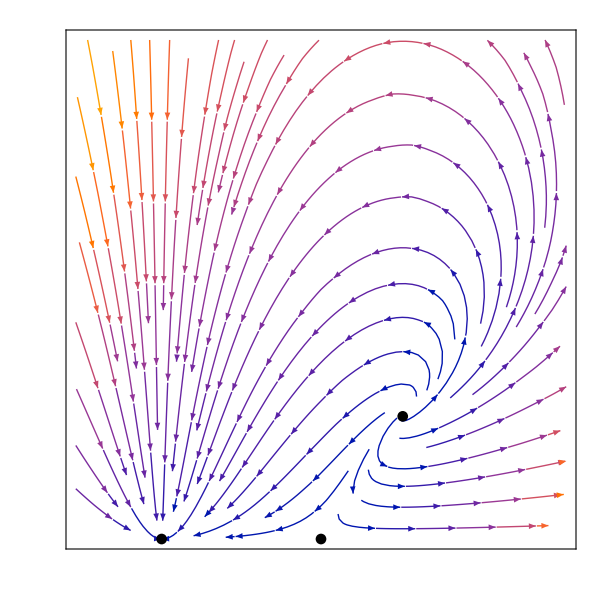

```mathematica
(*Show the plots of the phase space and fixed points together*)
Show[PhaseSpacexz,FPShowxz,FrameLabel->{MaTeX["x",FontSize->18],MaTeX["z",FontSize->18]},FrameTicks->{{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->18]},{z,0.5Range[-1,6]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,1Range[-1,5]}],None}},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotRange->{{-1,5},{0,3}},ImageSize->{600,600},PlotRangePadding->{0.08,0.08}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Parameter values are set such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
de1:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.0125 (6.+37. x+60. x^2)},{x→0.05,y→-0.129099,z→0.},{x→0.05,y→0.129099,z→0.},{x→2.,y→-0.816497,z→0.},{x→2.,y→0.816497,z→0.},{x→3.,y→-1.11617,z→0.7375},{x→3.,y→1.11617,z→0.7375}}

```mathematica
(*Extract the values for the fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
FP[7]={x/.FPs[[7,1]],y/.FPs[[7,2]],z/.FPs[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,7}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(y (-1.5375+1.5 x-1. z) | 0.075+0.75 x^2-1. x (1.5375+z) | -x y
0.0770833+0.25 x | -2 y | -1/6
y z | (-3+x) z | (-3+x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.0125 (6.+37. x+60. x^2)) | (0. | 0.075-1.6125 x+0.2875 x^2-0.75 x^3 | 0.
0.0770833+0.25 x | 0. | -1/6
0. | -0.225-1.3125 x-1.7875 x^2+0.75 x^3 | 0.) | (0
-√(0.0432812+0.113203 x-0.0830469 x^2-0.110937 x^3-0.1875 x^4)
√(0.0432812+0.113203 x-0.0830469 x^2-0.110937 x^3-0.1875 x^4)) | (0.666667/(0.308333+1. x) | 0 | 1.
-(1. (-0.0308333+0.562917 x+2.03181 x^2-0.075 x^3+1. x^4))/((0.308333+1. x) (-0.3-1.75 x-2.38333 x^2+1. x^3)) | -(1.33333 √(0.0432813+0.113203 x-0.0830469 x^2-0.110938 x^3-0.1875 x^4))/(-0.3-1.75 x-2.38333 x^2+1. x^3) | 1.
-(1. (-0.0308333+0.562917 x+2.03181 x^2-0.075 x^3+1. x^4))/((0.308333+1. x) (-0.3-1.75 x-2.38333 x^2+1. x^3)) | (1.33333 √(0.0432813+0.113203 x-0.0830469 x^2-0.110938 x^3-0.1875 x^4))/(-0.3-1.75 x-2.38333 x^2+1. x^3) | 1.)
(0.05
-0.129099
0.) | (0.188808 | 0. | 0.00645497
0.0895833 | 0.258199 | -1/6
0. | 0. | 0.380843) | (0.380843
0.258199
0.188808) | (0.0201538 | -0.800065 | 0.599574
0. | 1. | 0.
0.612372 | -0.790569 | 0.)
(0.05
0.129099
0.) | (-0.188808 | 0. | -0.00645497
0.0895833 | -0.258199 | -1/6
0. | 0. | -0.380843) | (-0.380843
-0.258199
-0.188808) | (0.0201538 | 0.800065 | 0.599574
0. | 1. | 0.
0.612372 | 0.790569 | 0.)
(2.
-0.816497
0.) | (-1.19413 | 0. | 1.63299
0.577083 | 1.63299 | -1/6
0. | 0. | 0.816497) | (1.63299
-1.19413
0.816497) | (0. | 1. | 0.
0.979796 | -0.2 | 0.
0.605959 | -0.275985 | 0.746087)
(2.
0.816497
0.) | (1.19413 | 0. | -1.63299
0.577083 | -1.63299 | -1/6
0. | 0. | -0.816497) | (-1.63299
1.19413
-0.816497) | (0. | 1. | 0.
0.979796 | 0.2 | 0.
0.605959 | 0.275985 | 0.746087)
(3.
-1.11617
0.7375) | (-2.48348 | -8.88178×10^-16 | 3.34851
0.827083 | 2.23234 | -1/6
-0.823175 | 0. | 0.) | (2.23234+0. ⅈ
-1.24174+1.10204 ⅈ
-1.24174-1.10204 ⅈ) | (-8.17767×10^-17+0. ⅈ | 1.+0. ⅈ | 1.5283×10^-16+0. ⅈ
0.880401+0. ⅈ | -0.180212-0.0432659 ⅈ | 0.326482+0.289752 ⅈ
0.880401+0. ⅈ | -0.180212+0.0432659 ⅈ | 0.326482-0.289752 ⅈ)
(3.
1.11617
0.7375) | (2.48348 | -8.88178×10^-16 | -3.34851
0.827083 | -2.23234 | -1/6
0.823175 | 0. | 0.) | (-2.23234+0. ⅈ
1.24174+1.10204 ⅈ
1.24174-1.10204 ⅈ) | (-8.17767×10^-17+0. ⅈ | -1.+0. ⅈ | 1.5283×10^-16+0. ⅈ
0.880401+0. ⅈ | 0.180212-0.0432659 ⅈ | 0.326482-0.289752 ⅈ
0.880401+0. ⅈ | 0.180212+0.0432659 ⅈ | 0.326482+0.289752 ⅈ)

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLine=ParametricPlot3D[{FP[1][[1]],FP[1][[2]],FP[1][[3]]},{x,0,15},PlotStyle->Red];
```

```mathematica
(*Plot the fixed points of the system*)
FPsxyz=ListPointPlot3D[Table[FP[i],{i,2,7}],PlotStyle->Black];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpacexyz=StreamPlot3D[{de1,de2,de3},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}];
```

```mathematica
(*Show the phase space and the fixed points together*)
Show[PhaseSpacexyz,FPsxyz,EinsteinPointLine]
```

-Graphics3D-

### Compactification

#### Compact x - z Phase Space

```mathematica
(*Parameter values are set such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, and dark matter, Z*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*Z/(1-Z)
deZ:=Z'=-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deZ==0},{X,Z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{X→0.047619,Z→0.},{X→0.666667,Z→0.},{X→0.75,Z→0.42446}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FP[1]={X/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Z/.FPs[[2,2]]};
FP[3]={X/.FPs[[3,1]],Z/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Z]}, {D[deZ,X],D[deZ,Z]}}];
J//MatrixForm
```

((1.6875-0.6875 Z+X (-4.725+2.725 Z))/(-1.+Z) | ((-1+X) X)/(-1+Z)^2
-((-1+Z) Z)/(-1+X)^2 | ((-3+4 X) (-1+2 Z))/(-1+X))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.047619
0.) | (-1.4625 | -0.0453515
0. | -2.95) | (-2.95
-1.4625) | (0.0304742 | 0.999536
1. | 0.)
(0.666667
0.) | (1.4625 | -0.222222
0. | -1.) | (1.4625
-1.) | (1. | 0.
0.0898773 | 0.995953)
(0.75
0.42446) | (2.225 | -0.566045
3.9087 | 0.) | (1.1125+0.987342 ⅈ
1.1125-0.987342 ⅈ) | (0.266011+0.236084 ⅈ | 0.934613+0. ⅈ
0.266011-0.236084 ⅈ | 0.934613+0. ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPShowCompactxz=ListPlot[FPs,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpaceCompactxz=StreamPlot[{deX,deZ},{X,-0.1,1},{Z,0,1},FrameLabel->{"X","Z"}];
```

```mathematica
(*Plot the curves where Z' = 0*)
ZLine=ContourPlot[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*Z/(1-Z)==0,{X,0,1},{Z,0,1},ContourStyle->Blue];
```

```mathematica
(*Plot the curves where X' = 0*)
XLine=ContourPlot[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)==0,{X,0,1},{Z,-0.1,1},ContourStyle->Red,PlotPoints->100];
```

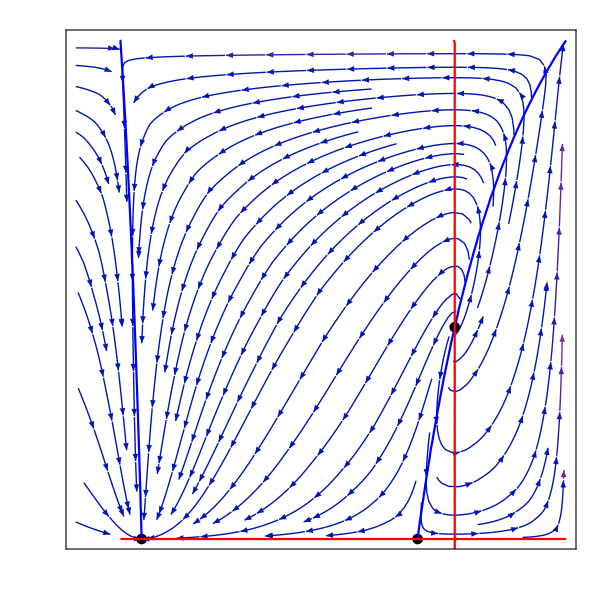

```mathematica
(*Show the phase space, fixed points and Z' = 0 and X' = 0 curves together*)
Show[PhaseSpaceCompactxz,FPShowCompactxz,ZLine,XLine,FrameLabel->{MaTeX["X",FontSize->18],MaTeX["Z",FontSize->18]},FrameTicks->{{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->18]},{X,0.2Range[-1,5]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->18]},{Z,0.2Range[0,5]}],None}},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotRange->{{-.1,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04}]
```

```mathematica
(*Evaluate X' at X = 0*)
(*X'(X = 0) > 0, therefore trajectories that are initially to the right of the X' = 0 curve will always satisy X > 0*)
deX/.X->0
```

0.075

#### Compact x - y - z Phase Space

```mathematica
(*Parameter values are set such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(6.+25. X+29. X^2)/(86.-135. X+109. X^2)},{X→0.666667,Y→-0.632456,Z→0.},{X→0.047619,Y→-0.128037,Z→0.},{X→-0.431034-0.145278 ⅈ,Y→0.,Z→0.},{X→-0.431034+0.145278 ⅈ,Y→0.,Z→0.},{X→0.047619,Y→0.128037,Z→0.},{X→0.666667,Y→0.632456,Z→0.},{X→0.75,Y→-0.744803,Z→0.42446},{X→0.75,Y→0.744803,Z→0.42446},{X→0.75,Y→0.,Z→0.891452}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FP[1]={X,Y/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Y/.FPs[[2,2]],Z/.FPs[[2,3]]};
FP[3]={X/.FPs[[3,1]],Y/.FPs[[3,2]],Z/.FPs[[3,3]]};
FP[4]={X/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]]};
FP[5]={X/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]]};
FP[6]={X/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]]};
FP[7]={X/.FPs[[9,1]],Y/.FPs[[9,2]],Z/.FPs[[9,3]]};
FP[8]={X/.FPs[[10,1]],Y/.FPs[[10,2]],Z/.FPs[[10,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,8}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
J//MatrixForm
```

((Y (1.6875-0.6875 Z+X (-4.725+2.725 Z)))/(√(1-Y^2) (-1.+Z)) | (0.075+X^2 (2.3625-1.3625 Z)+X (-1.6875+0.6875 Z)-0.075 Z)/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | ((-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
(0.172917 (0.445783+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.0375-2.5375 Z+Y^2 (-3.0375+3.5375 Z)+X (-3.84375+Y^2 (5.84375-6.84375 Z)+4.84375 Z)+X^2 (2.18125-2.68125 Z+Y^2 (-3.18125+3.68125 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+4 X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+4 X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(6.+25. X+29. X^2)/(86.-135. X+109. X^2)) | (0. | (0.075-1.9125 X+5.575 X^2-6.4625 X^3+2.725 X^4)/(1.-2. X+1. X^2) | 0.
(-0.0770833-0.172917 X)/(-1.+X)^3 | 0. | -(0.309401 (0.788991-1.23853 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.121202+0.101002 X-0.653144 X^2-0.262604 X^3+1.47462 X^4-0.781079 X^5)/((-1.+X) (0.788991-1.23853 X+1. X^2)^2) | 0.) | (0
-(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)
(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)) | (-(1.78931 (-1.+X)^3 (0.788991-1.23853 X+1. X^2)^2)/((0.445783+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | ((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | -((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.)
(0.666667
-0.632456
0.) | (-1.19413 | 0. | 0.181444
2.41384 | 1.63299 | -0.0774597
0. | 0. | 0.816497) | (1.63299
-1.19413
0.816497) | (0. | 1. | 0.
0.760506 | -0.649331 | 0.
0.0885881 | -0.168767 | 0.981667)
(0.047619
-0.128037
0.) | (0.188808 | 2.84523×10^-17 | 0.00585485
0.0963469 | 0.258199 | -0.162585
0. | 0. | 0.380843) | (0.380843
0.258199
0.188808) | (0.0185705 | -0.792875 | 0.609102
-6.61074×10^-16 | -1. | 0.
-0.584422 | 0.81145 | 0.)
(0.047619
0.128037
0.) | (-0.188808 | 2.84523×10^-17 | -0.00585485
0.0963469 | -0.258199 | -0.162585
0. | 0. | -0.380843) | (-0.380843
-0.258199
-0.188808) | (0.0185705 | 0.792875 | 0.609102
-6.61074×10^-16 | 1. | 0.
0.584422 | 0.81145 | 0.)
(0.666667
0.632456
0.) | (1.19413 | 0. | -0.181444
2.41384 | -1.63299 | -0.0774597
0. | 0. | -0.816497) | (-1.63299
1.19413
-0.816497) | (0. | 1. | 0.
0.760506 | 0.649331 | 0.
0.0885881 | 0.168767 | 0.981667)
(0.75
-0.744803
0.42446) | (-2.48348 | 0. | 0.631802
3.9319 | 2.23234 | -0.149497
-4.36277 | 0. | 0.) | (2.23234+0. ⅈ
-1.24174+1.10204 ⅈ
-1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061-0.222416 ⅈ | -0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061+0.222416 ⅈ | -0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.744803
0.42446) | (2.48348 | 0. | -0.631802
3.9319 | -2.23234 | -0.149497
4.36277 | 0. | 0.) | (-2.23234+0. ⅈ
1.24174+1.10204 ⅈ
1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061+0.222416 ⅈ | 0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061-0.222416 ⅈ | 0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.
0.891452) | (0. | -1.40156 | 0.
13.2333 | 0. | -14.145
0. | 0. | 0.) | (0.+4.30666 ⅈ
0.-4.30666 ⅈ
0.+0. ⅈ) | (0.-0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.+0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.730249+0. ⅈ | 0.+0. ⅈ | 0.683182+0. ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPShowXYZ=ListPointPlot3D[Table[FP[i],{i,2,7}], PlotStyle->{Black}];
```

```mathematica
(*Plot the extra fixed points from compactification*)
CompactFPShow=ListPointPlot3D[{{1,1,1},{1,-1,1},{0,1,1},{0,-1,1},{1,1,0},{1,-1,0},{0,1,0},{0,-1,0}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLineXYZ=ParametricPlot3D[{FP[1][[1]],FP[1][[2]],FP[1][[3]]},{X,0,1},{Z,0,1},PlotStyle->Directive[Red,Thickness[.01]]];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpaceXYZ=StreamPlot3D[{deX,deY,deZ},{X,0,1},{Y,-1,1},{Z,0,1},AxesLabel->{"X","Y","Z"}];
```

Min::nord: Invalid comparison with -1.57596-2.32827×10^-7 ⅈ attempted.

Max::nord: Invalid comparison with -1.57596-2.32827×10^-7 ⅈ attempted.

Min::nord: Invalid comparison with -1.52559+8.15036×10^-9 ⅈ attempted.

Max::nord: Invalid comparison with -1.52559+8.15036×10^-9 ⅈ attempted.

Min::nord: Invalid comparison with -1.44197+9.85289×10^-8 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Max::nord: Invalid comparison with -1.44197+9.85289×10^-8 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
(*Show the phase space and fixed points together*)
Show[PhaseSpaceXYZ,FPShowXYZ,CompactFPShow,EinsteinPointLineXYZ]
```

-Graphics3D-

## Compact Numeric Phase Spaces using Density Parameters for the Initial Conditions

### Ωk0 > 0 (Open Models)

#### Einstein Fixed Points

```mathematica
(*Parameter values are set such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define Ωk0 for open models using data from Planck 2018*)
Ωk0=0.003;
```

```mathematica
(*Define Ωm0 in terms of Ωx0 and Ωk0*)
Ωm0=1-Ωx0-Ωk0;
```

```mathematica
(*Define the initial conditions using the density parameters*)
(*K is defined as k/ρ* *)
x0=ℛ/α;
z0=Ωm0*ℛ/(Ωx0*α);
K=-Ωk0*ℛ/(3*α*Ωx0);
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z*)
dext:=x1'[t]==-3*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*z1[t]
dezt:=z1'[t]==-3*z1[t] + q*x1[t]*z1[t]
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajxz[Ωx0_]=NDSolve[{dext,dezt,x1[0]==x0,z1[0]==z0},{x1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (0.1 (0.997-1. Ωx0))/Ωx0 is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-0.25 x1[t]) (-0.05+x1[t])-x1[t] z1[t],z1'[t]==-3 z1[t]+x1[t] z1[t],x1[0]==0.1,z1[0]==(0.1 (0.997-Ωx0))/Ωx0},{x1,z1},{t,-100,100}]

```mathematica
(*Solve for the initial conditions plotted above*)
```

```mathematica
sol[1]=trajxz[0.6889]
sol[2]=trajxz[0.1]
sol[3]=trajxz[0.95]
```

{{x1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

{{x1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

{{x1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Define a reduced array to find the first Einstein point around x = ℛ*)
xTableSol1xℛ=Table[x1[i]/.sol[1],{i,-1,100,.01}];
zTableSol1xℛ=Table[z1[i]/.sol[1],{i,-1,100,.01}];

xTableSol2xℛ=Table[x1[i]/.sol[2],{i,0,100,.01}];
zTableSol2xℛ=Table[z1[i]/.sol[2],{i,0,100,.01}];
```

```mathematica
(*Using the reduced arrays of x and z found numerically, solve the equation to find the remaining Einstein fixed points*)
EinsteinPlotValuesSol1xℛ=(zTableSol1xℛ)+(xTableSol1xℛ)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1xℛ)^2;
EinsteinPlotValuesSol2xℛ=(zTableSol2xℛ)+(xTableSol2xℛ)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2xℛ)^2;
```

```mathematica
(*Find the value closest to zero in each array to find the Einstein points closest to x = ℛ*)
NearestToZero1xℛ=Flatten[Nearest[EinsteinPlotValuesSol1xℛ,0]]
NearestToZero2xℛ=Flatten[Nearest[EinsteinPlotValuesSol2xℛ,0]]
```

{0.00137833}

{-0.00107936}

```mathematica
(*Find the position of the values closest to zero in the array*)
PositionNearestToZero1xℛ=Flatten[Position[EinsteinPlotValuesSol1xℛ,NearestToZero1xℛ]];
PositionNearestToZero2xℛ=Flatten[Position[EinsteinPlotValuesSol2xℛ,NearestToZero2xℛ]];
```

```mathematica
(*Find the corresponding x and z values to find the Einstein points*)
EinsteinPointOpenSol1xℛi=Flatten[{xTableSol1xℛ[[PositionNearestToZero1xℛ]],0,zTableSol1xℛ[[PositionNearestToZero1xℛ]]}]
EinsteinPointOpenSol2xℛi=Flatten[{xTableSol2xℛ[[PositionNearestToZero2xℛ]],0,zTableSol2xℛ[[PositionNearestToZero2xℛ]]}]
```

{0.150956,0,0.163286}

{0.0568706,0,0.102649}

```mathematica
(*Express the Einstein fixed points in terms of compactified variables*)
EinsteinPointOpenSol1i=Flatten[{xTableSol1xℛ[[PositionNearestToZero1xℛ]]/(1+xTableSol1xℛ[[PositionNearestToZero1xℛ]]),0,zTableSol1xℛ[[PositionNearestToZero1xℛ]]/(1+zTableSol1xℛ[[PositionNearestToZero1xℛ]])}]
EinsteinPointOpenSol2i=Flatten[{xTableSol2xℛ[[PositionNearestToZero2xℛ]]/(1+xTableSol2xℛ[[PositionNearestToZero2xℛ]]),0,zTableSol2xℛ[[PositionNearestToZero2xℛ]]/(1+zTableSol2xℛ[[PositionNearestToZero2xℛ]])}]
```

{0.131157,0,0.140366}

{0.0538104,0,0.0930931}

```mathematica
(*Define a reduced array to find the second Einstein point*)
xTableSol1=Table[x1[i]/.sol[1],{i,-3,-1.5,.001}];
zTableSol1=Table[z1[i]/.sol[1],{i,-3,-1.5,.001}];

xTableSol2=Table[x1[i]/.sol[2],{i,-3,-0.7,.001}];
zTableSol2=Table[z1[i]/.sol[2],{i,-3,-0.7,.001}];
```

```mathematica
(*Using the reduced arrays of x and z found numerically, solve the equation to find the remaining Einstein fixed points*)
EinsteinPlotValuesSol1=(zTableSol1)+(xTableSol1)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1)^2;
EinsteinPlotValuesSol2=(zTableSol2)+(xTableSol2)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2)^2;
```

```mathematica
(*Find the value closest to zero in each array to find the remaining Einstein points*)
NearestToZero1=Flatten[Nearest[EinsteinPlotValuesSol1,0]];
NearestToZero2=Flatten[Nearest[EinsteinPlotValuesSol2,0]];
```

```mathematica
(*Find the position of the value closest to zero in the array*)
PositionNearestToZero1=Flatten[Position[EinsteinPlotValuesSol1,NearestToZero1]];
PositionNearestToZero2=Flatten[Position[EinsteinPlotValuesSol2,NearestToZero2]];
```

```mathematica
(*Find the corresponding x and z values to find the Einstein points*)
EinsteinPointOpenSol1ii=Flatten[{xTableSol1[[PositionNearestToZero1]],0,zTableSol1[[PositionNearestToZero1]]}]
EinsteinPointOpenSol2ii=Flatten[{xTableSol2[[PositionNearestToZero2]],0,zTableSol2[[PositionNearestToZero2]]}]
```

{1.72366,0,3.10415}

{2.61882,0,6.44827}

```mathematica
(*Express the Einstein fixed points in terms of compactified variables*)
EinsteinPointOpenSol1ii=Flatten[{xTableSol1[[PositionNearestToZero1]]/(1+xTableSol1[[PositionNearestToZero1]]),0,zTableSol1[[PositionNearestToZero1]]/(1+zTableSol1[[PositionNearestToZero1]])}]
EinsteinPointOpenSol2ii=Flatten[{xTableSol2[[PositionNearestToZero2]]/(1+xTableSol2[[PositionNearestToZero2]]),0,zTableSol2[[PositionNearestToZero2]]/(1+zTableSol2[[PositionNearestToZero2]])}]
```

{0.632847,0,0.756344}

{0.723667,0,0.865741}

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
xTableSol1Full=Table[x1[i]/.sol[1],{i,-100,100,.1}];
zTableSol1Full=Table[z1[i]/.sol[1],{i,-100,100,.1}];

xTableSol2Full=Table[x1[i]/.sol[2],{i,-100,100,.1}];
zTableSol2Full=Table[z1[i]/.sol[2],{i,-100,100,.1}];

xTableSol3Full=Table[x1[i]/.sol[3],{i,-100,100,.1}];
zTableSol3Full=Table[z1[i]/.sol[3],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSol1Full=(zTableSol1Full)+(xTableSol1Full)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1Full)^2;
EinsteinPlotValuesSol2Full=(zTableSol2Full)+(xTableSol2Full)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2Full)^2;
EinsteinPlotValuesSol3Full=(zTableSol3Full)+(xTableSol3Full)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol3Full)^2;
```

```mathematica
(*Merge the xTable values and the EinsteinPlotValueSol values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsSol1Full=MapThread[h,{xTableSol1Full,EinsteinPlotValuesSol1Full}];
EinsteinPointSolutionsSol2Full=MapThread[h,{xTableSol2Full,EinsteinPlotValuesSol2Full}];
EinsteinPointSolutionsSol3Full=MapThread[h,{xTableSol3Full,EinsteinPlotValuesSol3Full}];
```

```mathematica
(*Plot each solution for each initial condition*)
EinsteinPlot[1]=ListPlot[EinsteinPointSolutionsSol1Full];
EinsteinPlot[2]=ListPlot[EinsteinPointSolutionsSol2Full];
EinsteinPlot[3]=ListPlot[EinsteinPointSolutionsSol3Full];
```

```mathematica
(*Put the plots into a table*)
EinsteinPlots=Table[EinsteinPlot[i],{i,1,3}];
```

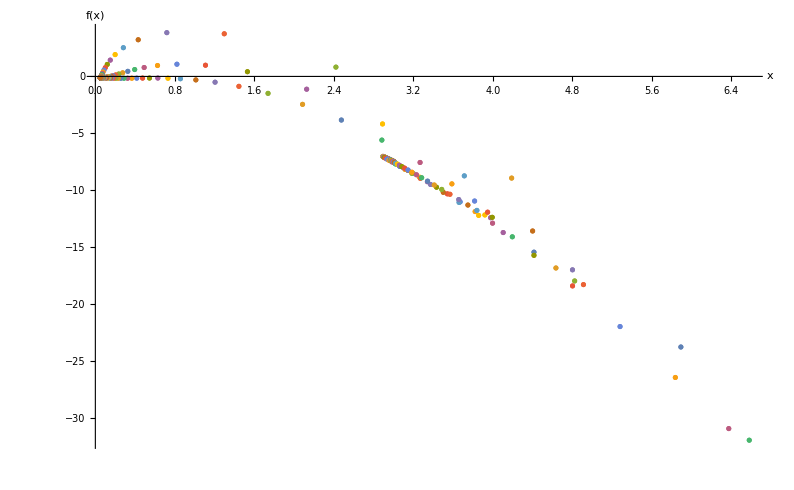

```mathematica
(*Show the plots on the same axes*)
(*When the curves cross f(x) = 0, an Einstein fixed point exists*)
Show[EinsteinPlots,PlotRange->Full,AxesLabel->{"x","f(x)"}]
```

#### 3-D Phase Space

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))+q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
(*β sets the sign of the square root in Y0*) 
trajOpen[Ωx0_,β_]=NDSolve[{deXt,deYt,deZt, X1[0]==x0/(1+x0),Y1[0]==β*y0/Sqrt[1+y0^2],Z1[0]==z0/(1+z0)}, {X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (β √(0.0333333+0.0001/Ωx0+(0.0333333 (0.997-1. Ωx0))/Ωx0))/(√(1.03333+0.0001/Ωx0+(0.0333333 (0.997-1. Ωx0))/Ωx0)) is not a number or a rectangular array of numbers.

```mathematica
(*Solve for different initial conditions*)
```

```mathematica
sol[1]=trajOpen[0.6889,1]
sol[2]=trajOpen[0.1,1]
sol[3]=trajOpen[0.95,1]
```

NDSolve::mxst: Maximum number of 237477 steps reached at the point t == -7.02577.

{{X1→InterpolatingFunction[{{-7.02577, 100.}}, <>],Y1→InterpolatingFunction[{{-7.02577, 100.}}, <>],Z1→InterpolatingFunction[{{-7.02577, 100.}}, <>]}}

NDSolve::mxst: Maximum number of 1992232 steps reached at the point t == -4.04113.

{{X1→InterpolatingFunction[{{-4.04113, 100.}}, <>],Y1→InterpolatingFunction[{{-4.04113, 100.}}, <>],Z1→InterpolatingFunction[{{-4.04113, 100.}}, <>]}}

NDSolve::mxst: Maximum number of 131308 steps reached at the point t == -9.04763.

{{X1→InterpolatingFunction[{{-9.04763, 100.}}, <>],Y1→InterpolatingFunction[{{-9.04763, 100.}}, <>],Z1→InterpolatingFunction[{{-9.04763, 100.}}, <>]}}

```mathematica
sol[4]=trajOpen[0.6889,-1]
sol[5]=trajOpen[0.1,-1]
sol[6]=trajOpen[0.95,-1]
```

NDSolve::mxst: Maximum number of 237477 steps reached at the point t == 6.85064.

{{X1→InterpolatingFunction[{{-100., 6.85064}}, <>],Y1→InterpolatingFunction[{{-100., 6.85064}}, <>],Z1→InterpolatingFunction[{{-100., 6.85064}}, <>]}}

NDSolve::mxst: Maximum number of 1992232 steps reached at the point t == 3.86855.

{{X1→InterpolatingFunction[{{-100., 3.86855}}, <>],Y1→InterpolatingFunction[{{-100., 3.86855}}, <>],Z1→InterpolatingFunction[{{-100., 3.86855}}, <>]}}

NDSolve::mxst: Maximum number of 131308 steps reached at the point t == 9.15025.

{{X1→InterpolatingFunction[{{-100., 9.15025}}, <>],Y1→InterpolatingFunction[{{-100., 9.15025}}, <>],Z1→InterpolatingFunction[{{-100., 9.15025}}, <>]}}

```mathematica
(*Plot each trajectory*)
```

```mathematica
PhaseSpaceXYZOpen[1]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[1],{t,-7,100},PlotStyle -> {{Darker[Blue], Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
PhaseSpaceXYZOpen[2]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[2],{t,-4,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
PhaseSpaceXYZOpen[3]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[3], {t,-9,100},PlotStyle -> {{Magenta, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
PhaseSpaceXYZOpen[4]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[4],{t,-100,6.8},PlotStyle -> {{Darker[Blue], Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
PhaseSpaceXYZOpen[5]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[5],{t,-100,3.8},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->10000];
```

```mathematica
PhaseSpaceXYZOpen[6]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[6],{t,-100,9},PlotStyle -> {{Magenta, Opacity[0.75]}}],PlotPoints->10000];
```

```mathematica
(*Put the plots of the trajectories into a table*)
PhaseSpaceXYZOpen=Table[PhaseSpaceXYZOpen[i],{i,1,6}];
```

```mathematica
(*Define the equation for the Flat Friedmann Separatrix (FFS)*)
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
(*Plot the FFS*)
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
(*The region above this surface is accelerating, and below is decelerating*)
AccnXYZ=ContourPlot3D[-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{X,0,1},{Y,-1,1},{Z,0,1},Mesh->None,ContourStyle->{Red,Opacity[0.2]}];
```

```mathematica
(*Plot the de Sitter line going through the two spiral fixed points*)
dSLine=ParametricPlot3D[{FP[6][[1]],Y,FP[6][[3]]},{X,0,1},{Y,-1,1},PlotPoints->100,PlotStyle->{{Black,Thickness[0.01]}}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinPointsOpen=ListPointPlot3D[{EinsteinPointOpenSol1i,EinsteinPointOpenSol1ii,EinsteinPointOpenSol2i,EinsteinPointOpenSol2ii},PlotStyle->Black];
```

```mathematica
(*Show the trajectories, the fixed points, the FFS and the boundary between accelerating and decelerating regions together*)
Show[PhaseSpaceXYZOpen,dSLine,FFSPlus,FFSMinus,AccnXYZ,FPShowXYZ,CompactFPShow,EinsteinPointLineXYZ,EinsteinPointsOpen,Axes->True,Frame->False,AxesLabel->{MaTeX["X",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["Z",FontSize->20]},Ticks->{{0.0,0.5,1.0},{-1.0,-0.5,0.0,0.5,1.0},{0.0,0.5,1.0}},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400}]
```

-Graphics3D-

#### 2-D Z - X Projection

```mathematica
(*Plot the trajectories define above on the Z-X plane*)
```

```mathematica
PhaseSpaceXZOpen[1]=ParametricPlot[Evaluate[{Z1[t],X1[t]}/.sol[1],{t,-7,100},PlotStyle -> {{Darker[Blue], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceXZOpen[2]=ParametricPlot[Evaluate[{Z1[t],X1[t]}/.sol[2],{t,-4,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpaceXZOpen[3]=ParametricPlot[Evaluate[{Z1[t],X1[t]}/.sol[3],{t,-8.9,100},PlotStyle -> {{Magenta, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
PhaseSpaceXZOpen=Table[PhaseSpaceXZOpen[i],{i,1,3}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions on the Z-X plane*)
AccnXZ=ContourPlot[-(1/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{Z,0,1},{X,0,1},ContourStyle->{Red,Opacity[0.8]},PlotPoints->200];
```

```mathematica
(*Define the Einstein fixed points in the Z-X plane*)
EinsteinPointOpenZXSol1i=Flatten[{zTableSol1xℛ[[PositionNearestToZero1xℛ]]/(1+zTableSol1xℛ[[PositionNearestToZero1xℛ]]),xTableSol1xℛ[[PositionNearestToZero1xℛ]]/(1+xTableSol1xℛ[[PositionNearestToZero1xℛ]])}];
EinsteinPointOpenZXSol2i=Flatten[{zTableSol2xℛ[[PositionNearestToZero2xℛ]]/(1+zTableSol2xℛ[[PositionNearestToZero2xℛ]]),xTableSol2xℛ[[PositionNearestToZero2xℛ]]/(1+xTableSol2xℛ[[PositionNearestToZero2xℛ]])}];

EinsteinPointOpenZXSol1ii=Flatten[{zTableSol1[[PositionNearestToZero1]]/(1+zTableSol1[[PositionNearestToZero1]]),xTableSol1[[PositionNearestToZero1]]/(1+xTableSol1[[PositionNearestToZero1]])}]
EinsteinPointOpenZXSol2ii=Flatten[{zTableSol2[[PositionNearestToZero2]]/(1+zTableSol2[[PositionNearestToZero2]]),xTableSol2[[PositionNearestToZero2]]/(1+xTableSol2[[PositionNearestToZero2]])}]
```

{0.756344,0.632847}

{0.865741,0.723667}

```mathematica
EinsteinPointsZXOpen=ListPlot[{EinsteinPointOpenZXSol1i,EinsteinPointOpenZXSol1ii,EinsteinPointOpenZXSol2i,EinsteinPointOpenZXSol2ii},PlotStyle->Black];
```

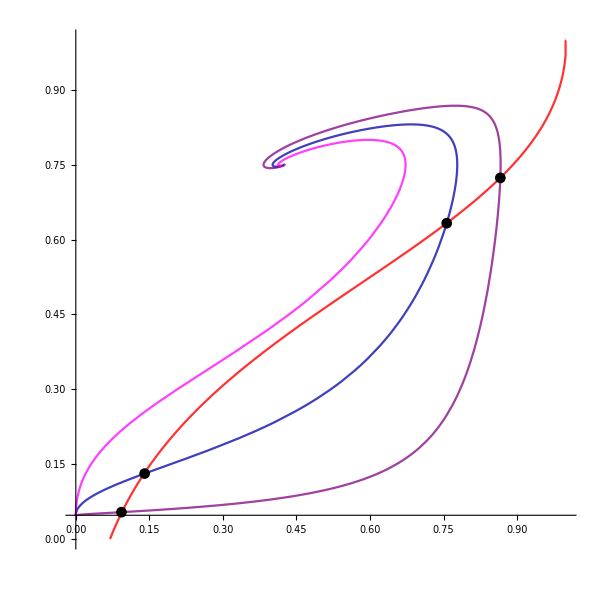

```mathematica
(*Show the trajectories and the boundary between accelerating and decelerating regions together*)
Show[PhaseSpaceXZOpen,AccnXZ,EinsteinPointsZXOpen,Axes->True,Frame->False,AxesLabel->{MaTeX["Z",FontSize->18],MaTeX["X",FontSize->18]},FrameTicks->{{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->18]},{Z,0.2Range[-1,5]}],None},{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->18]},{X,0.2Range[-1,5]}],None}},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotRange->{{0,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.08,0.08}]
```

### Ωk0 < 0 (Closed Models)

#### Einstein Fixed Points

```mathematica
(*Parameter values are set such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define Ωk0 for open models using data from Planck 2018*)
Ωk0=-0.001;
```

```mathematica
(*Define Ωm0 in terms of Ωx0 and Ωk0*)
Ωm0=1-Ωx0-Ωk0;
```

```mathematica
(*Define the initial conditions using the density parameters*)
(*K is defined as k/ρ* *)
x0=ℛ/α;
z0=Ωm0*ℛ/(Ωx0*α);
K=-Ωk0*ℛ/(3*α*Ωx0);
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Set a value for α, which sets the value of teh low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z*)
dext:=x1'[t]==-3*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*z1[t]
dezt:=z1'[t]==-3*z1[t] + q*x1[t]*z1[t]
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajxz[Ωx0_]=NDSolve[{dext,dezt,x1[0]==x0,z1[0]==z0},{x1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (0.1 (1.001-1. Ωx0))/Ωx0 is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-0.25 x1[t]) (-0.05+x1[t])-x1[t] z1[t],z1'[t]==-3 z1[t]+x1[t] z1[t],x1[0]==0.1,z1[0]==(0.1 (1.001-Ωx0))/Ωx0},{x1,z1},{t,-100,100}]

```mathematica
(*Solve for the initial conditions plotted above*)
```

```mathematica
sol[1]=trajxz[0.6889]
sol[2]=trajxz[0.1]
sol[3]=trajxz[0.95]
```

{{x1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

{{x1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

{{x1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Define a reduced array to find the first Einstein point around x = ℛ*)
xTableSol1xℛ=Table[x1[i]/.sol[1],{i,-1,100,.01}];
zTableSol1xℛ=Table[z1[i]/.sol[1],{i,-1,100,.01}];

xTableSol2xℛ=Table[x1[i]/.sol[2],{i,0,100,.01}];
zTableSol2xℛ=Table[z1[i]/.sol[2],{i,0,100,.01}];
```

```mathematica
(*Using the reduced arrays of x and z found numerically, solve the equation to find the remaining Einstein fixed points*)
EinsteinPlotValuesSol1xℛ=(zTableSol1xℛ)+(xTableSol1xℛ)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1xℛ)^2;
EinsteinPlotValuesSol2xℛ=(zTableSol2xℛ)+(xTableSol2xℛ)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2xℛ)^2;
```

```mathematica
(*Find the value closest to zero in each array to find the Einstein points closest to x = ℛ*)
NearestToZero1xℛ=Flatten[Nearest[EinsteinPlotValuesSol1xℛ,0]]
NearestToZero2xℛ=Flatten[Nearest[EinsteinPlotValuesSol2xℛ,0]]
```

{-0.0000868777}

{-0.000602539}

```mathematica
(*Find the position of the values closest to zero in the array*)
PositionNearestToZero1xℛ=Flatten[Position[EinsteinPlotValuesSol1xℛ,NearestToZero1xℛ]];
PositionNearestToZero2xℛ=Flatten[Position[EinsteinPlotValuesSol2xℛ,NearestToZero2xℛ]];
```

```mathematica
(*Find the corresponding x and z values to find the Einstein points*)
EinsteinPointClosedSol1xℛi=Flatten[{xTableSol1xℛ[[PositionNearestToZero1xℛ]],0,zTableSol1xℛ[[PositionNearestToZero1xℛ]]}]
EinsteinPointClosedSol2xℛi=Flatten[{xTableSol2xℛ[[PositionNearestToZero2xℛ]],0,zTableSol2xℛ[[PositionNearestToZero2xℛ]]}]
```

{0.149409,0,0.160757}

{0.0568301,0,0.103104}

```mathematica
(*Express the Einstein fixed points in terms of compactified variables*)
EinsteinPointClosedSol1i=Flatten[{xTableSol1xℛ[[PositionNearestToZero1xℛ]]/(1+xTableSol1xℛ[[PositionNearestToZero1xℛ]]),0,zTableSol1xℛ[[PositionNearestToZero1xℛ]]/(1+zTableSol1xℛ[[PositionNearestToZero1xℛ]])}]
EinsteinPointClosedSol2i=Flatten[{xTableSol2xℛ[[PositionNearestToZero2xℛ]]/(1+xTableSol2xℛ[[PositionNearestToZero2xℛ]]),0,zTableSol2xℛ[[PositionNearestToZero2xℛ]]/(1+zTableSol2xℛ[[PositionNearestToZero2xℛ]])}]
```

{0.129987,0,0.138493}

{0.0537741,0,0.0934669}

```mathematica
(*Define a reduced array to find the second Einstein point*)
xTableSol1=Table[x1[i]/.sol[1],{i,-3,-1.5,.001}];
zTableSol1=Table[z1[i]/.sol[1],{i,-3,-1.5,.001}];

xTableSol2=Table[x1[i]/.sol[2],{i,-3,-0.7,.001}];
zTableSol2=Table[z1[i]/.sol[2],{i,-3,-0.7,.001}];
```

```mathematica
(*Using the reduced arrays of x and z found numerically, solve the equation to find the remaining Einstein fixed points*)
EinsteinPlotValuesSol1=(zTableSol1)+(xTableSol1)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1)^2;
EinsteinPlotValuesSol2=(zTableSol2)+(xTableSol2)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2)^2;
```

```mathematica
(*Find the value closest to zero in each array to find the remaining Einstein points*)
NearestToZero1=Flatten[Nearest[EinsteinPlotValuesSol1,0]];
NearestToZero2=Flatten[Nearest[EinsteinPlotValuesSol2,0]];
```

```mathematica
(*Find the position of the value closest to zero in the array*)
PositionNearestToZero1=Flatten[Position[EinsteinPlotValuesSol1,NearestToZero1]];
PositionNearestToZero2=Flatten[Position[EinsteinPlotValuesSol2,NearestToZero2]];
```

```mathematica
(*Find the corresponding x and z values to find the Einstein points*)
EinsteinPointClosedSol1ii=Flatten[{xTableSol1[[PositionNearestToZero1]],0,zTableSol1[[PositionNearestToZero1]]}]
EinsteinPointClosedSol2ii=Flatten[{xTableSol2[[PositionNearestToZero2]],0,zTableSol2[[PositionNearestToZero2]]}]
```

{1.72876,0,3.11737}

{2.6239,0,6.45603}

```mathematica
(*Express the Einstein fixed points in terms of compactified variables*)
EinsteinPointClosedSol1ii=Flatten[{xTableSol1[[PositionNearestToZero1]]/(1+xTableSol1[[PositionNearestToZero1]]),0,zTableSol1[[PositionNearestToZero1]]/(1+zTableSol1[[PositionNearestToZero1]])}]
EinsteinPointClosedSol2ii=Flatten[{xTableSol2[[PositionNearestToZero2]]/(1+xTableSol2[[PositionNearestToZero2]]),0,zTableSol2[[PositionNearestToZero2]]/(1+zTableSol2[[PositionNearestToZero2]])}]
```

{0.633534,0,0.757127}

{0.724054,0,0.86588}

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
xTableSol1Full=Table[x1[i]/.sol[1],{i,-100,100,.1}];
zTableSol1Full=Table[z1[i]/.sol[1],{i,-100,100,.1}];

xTableSol2Full=Table[x1[i]/.sol[2],{i,-100,100,.1}];
zTableSol2Full=Table[z1[i]/.sol[2],{i,-100,100,.1}];

xTableSol3Full=Table[x1[i]/.sol[3],{i,-100,100,.1}];
zTableSol3Full=Table[z1[i]/.sol[3],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSol1Full=(zTableSol1Full)+(xTableSol1Full)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1Full)^2;
EinsteinPlotValuesSol2Full=(zTableSol2Full)+(xTableSol2Full)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2Full)^2;
EinsteinPlotValuesSol3Full=(zTableSol3Full)+(xTableSol3Full)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol3Full)^2;
```

```mathematica
(*Merge the xTable values and the EinsteinPlotValueSol values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsSol1Full=MapThread[h,{xTableSol1Full,EinsteinPlotValuesSol1Full}];
EinsteinPointSolutionsSol2Full=MapThread[h,{xTableSol2Full,EinsteinPlotValuesSol2Full}];
EinsteinPointSolutionsSol3Full=MapThread[h,{xTableSol3Full,EinsteinPlotValuesSol3Full}];
```

```mathematica
(*Plot each solution for each initial condition*)
EinsteinPlot[1]=ListPlot[EinsteinPointSolutionsSol1Full];
EinsteinPlot[2]=ListPlot[EinsteinPointSolutionsSol2Full];
EinsteinPlot[3]=ListPlot[EinsteinPointSolutionsSol3Full];
```

```mathematica
(*Put the plots into a table*)
EinsteinPlots=Table[EinsteinPlot[i],{i,1,3}];
```

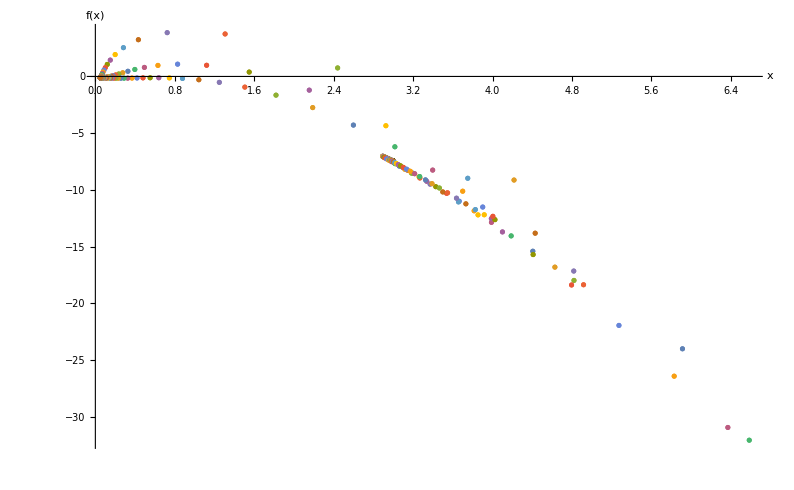

```mathematica
(*Show the plots on the same axes*)
(*When the curves cross f(x) = 0, an Einstein fixed point exists*)
Show[EinsteinPlots,PlotRange->Full,AxesLabel->{"x","f(x)"}]
```

#### 3-D Phase Space

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))+q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
(*β sets the sign of the square root in Y0*) 
trajClosed[Ωx0_,β_]=NDSolve[{deXt,deYt,deZt, X1[0]==x0/(1+x0),Y1[0]==β*y0/Sqrt[1+y0^2],Z1[0]==z0/(1+z0)}, {X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (β √(0.0333333-0.0000333333/Ωx0+(0.0333333 (1.001-1. Ωx0))/Ωx0))/(√(1.03333-0.0000333333/Ωx0+(0.0333333 (1.001-1. Ωx0))/Ωx0)) is not a number or a rectangular array of numbers.

```mathematica
(*Solve for different initial conditions*)
```

```mathematica
sol[1]=trajClosed[0.6889,1]
sol[2]=trajClosed[0.1,1]
sol[3]=trajClosed[0.95,1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot each trajectory*)
```

```mathematica
PhaseSpaceXYZClosed[1]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[1],{t,-100,100},PlotStyle -> {{Darker[Blue], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpaceXYZClosed[2]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpaceXYZClosed[3]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[3], {t,-100,100},PlotStyle -> {{Magenta, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
PhaseSpaceXYZClosed=Table[PhaseSpaceXYZClosed[i],{i,1,3}];
```

```mathematica
(*Define the equation for the Flat Friedmann Separatrix (FFS)*)
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
(*Plot the FFS*)
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
(*The region above this surface is accelerating, and below is decelerating*)
AccnXYZ=ContourPlot3D[-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{X,0,1},{Y,-1,1},{Z,0,1},Mesh->None,ContourStyle->{Red,Opacity[0.2]}];
```

```mathematica
(*Plot the de Sitter line going through the two spiral fixed points*)
dSLine=ParametricPlot3D[{FP[6][[1]],Y,FP[6][[3]]},{X,0,1},{Y,-1,1},PlotPoints->100,PlotStyle->{{Black,Thickness[0.01]}}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinPointsClosed=ListPointPlot3D[{EinsteinPointClosedSol1i,EinsteinPointClosedSol1ii,EinsteinPointClosedSol2i,EinsteinPointClosedSol2ii},PlotStyle->Black];
```

```mathematica
(*Show the trajectories, the fixed points, the FFS and the boundary between accelerating and decelerating regions together*)
Show[PhaseSpaceXYZClosed,dSLine,FFSPlus,FFSMinus,AccnXYZ,FPShowXYZ,CompactFPShow,EinsteinPointLineXYZ,EinsteinPointsClosed,PlotRange->{{0,1},{-1,1},{0,1}},AxesLabel->{MaTeX["X",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["Z",FontSize->20]},Ticks->{{0.0,0.5,1.0},{-1.0,-0.5,0.0,0.5,1.0},{0.0,0.5,1.0}},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400}]
```

-Graphics3D-

#### 2-D Z - X Projection

```mathematica
(*Plot the trajectories define above on the Z-X plane*)
```

```mathematica
PhaseSpaceXZClosed[1]=ParametricPlot[Evaluate[{Z1[t],X1[t]}/.sol[1],{t,-100,100},PlotStyle -> {{Darker[Blue], Opacity[0.75]}}],AxesLabel->{"Z","X"},PlotPoints->500];
```

```mathematica
PhaseSpaceXZClosed[2]=ParametricPlot[Evaluate[{Z1[t],X1[t]}/.sol[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"Z","X"},PlotPoints->500];
```

```mathematica
PhaseSpaceXZClosed[3]=ParametricPlot[Evaluate[{Z1[t],X1[t]}/.sol[3], {t,-100,100},PlotStyle -> {{Magenta, Opacity[0.75]}}],AxesLabel->{"Z","X"},PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
PhaseSpaceXZClosed=Table[PhaseSpaceXZClosed[i],{i,1,3}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions on the Z-X plane*)
AccnXZ=ContourPlot[-(1/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{Z,0,1},{X,0,1},ContourStyle->{Red,Opacity[0.8]},PlotPoints->200];
```

```mathematica
(*Define the Einstein fixed points in the Z-X plane*)
EinsteinPointClosedZXSol1i=Flatten[{zTableSol1xℛ[[PositionNearestToZero1xℛ]]/(1+zTableSol1xℛ[[PositionNearestToZero1xℛ]]),xTableSol1xℛ[[PositionNearestToZero1xℛ]]/(1+xTableSol1xℛ[[PositionNearestToZero1xℛ]])}];
EinsteinPointClosedZXSol2i=Flatten[{zTableSol2xℛ[[PositionNearestToZero2xℛ]]/(1+zTableSol2xℛ[[PositionNearestToZero2xℛ]]),xTableSol2xℛ[[PositionNearestToZero2xℛ]]/(1+xTableSol2xℛ[[PositionNearestToZero2xℛ]])}];

EinsteinPointClosedZXSol1ii=Flatten[{zTableSol1[[PositionNearestToZero1]]/(1+zTableSol1[[PositionNearestToZero1]]),xTableSol1[[PositionNearestToZero1]]/(1+xTableSol1[[PositionNearestToZero1]])}]
EinsteinPointClosedZXSol2ii=Flatten[{zTableSol2[[PositionNearestToZero2]]/(1+zTableSol2[[PositionNearestToZero2]]),xTableSol2[[PositionNearestToZero2]]/(1+xTableSol2[[PositionNearestToZero2]])}]
```

{0.757127,0.633534}

{0.86588,0.724054}

```mathematica
EinsteinPointsZXClosed=ListPlot[{EinsteinPointClosedZXSol1i,EinsteinPointClosedZXSol1ii,EinsteinPointClosedZXSol2i,EinsteinPointClosedZXSol2ii},PlotStyle->Black];
```

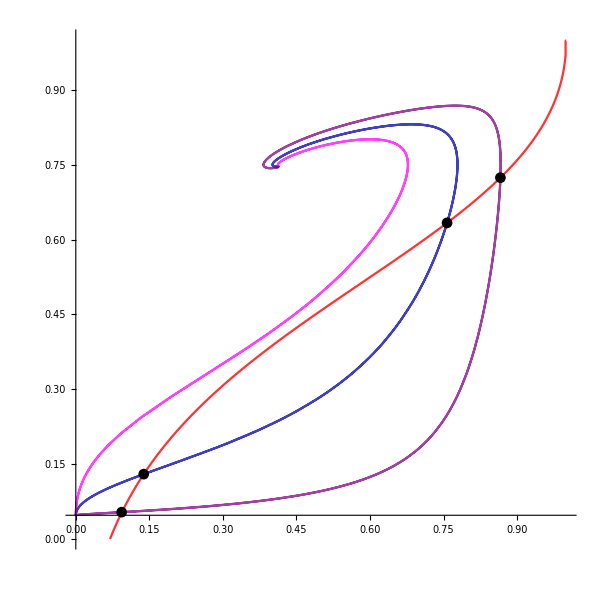

```mathematica
(*Show the trajectories and the boundary between accelerating and decelerating regions together*)
Show[PhaseSpaceXZClosed,AccnXZ,EinsteinPointsZXClosed,PlotRange->{{0,1},{0,1}},Axes->True,Frame->False,AxesLabel->{MaTeX["Z",FontSize->18],MaTeX["X",FontSize->18]},FrameTicks->{{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->18]},{Z,0.2Range[-1,5]}],None},{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->18]},{X,0.2Range[-1,5]}],None}},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotRange->{{0,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.08,0.08}]
```

### Ωk0 = 0 (Flat Models)

#### Einstein Fixed Points

```mathematica
(*Parameter values are set such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define Ωk0 for open models using data from Planck 2018*)
Ωk0=0;
```

```mathematica
(*Define Ωm0 in terms of Ωx0 and Ωk0*)
Ωm0=1-Ωx0-Ωk0;
```

```mathematica
(*Define the initial conditions using the density parameters*)
(*K is defined as k/ρ* *)
x0=ℛ/α;
z0=Ωm0*ℛ/(Ωx0*α);
K=-Ωk0*ℛ/(3*α*Ωx0);
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Set a value for α, which sets the value of teh low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z*)
dext:=x1'[t]==-3*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*z1[t]
dezt:=z1'[t]==-3*z1[t] + q*x1[t]*z1[t]
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajxz[Ωx0_]=NDSolve[{dext,dezt,x1[0]==x0,z1[0]==z0},{x1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (0.1 (1.-1. Ωx0))/Ωx0 is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-0.25 x1[t]) (-0.05+x1[t])-x1[t] z1[t],z1'[t]==-3 z1[t]+x1[t] z1[t],x1[0]==0.1,z1[0]==(0.1 (1-Ωx0))/Ωx0},{x1,z1},{t,-100,100}]

```mathematica
(*Solve for the initial conditions plotted above*)
```

```mathematica
sol[1]=trajxz[0.6889]
sol[2]=trajxz[0.1]
sol[3]=trajxz[0.95]
```

{{x1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

{{x1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

{{x1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
(*Define a reduced array to find the first Einstein point around x = ℛ*)
xTableSol1xℛ=Table[x1[i]/.sol[1],{i,-1,100,.01}];
zTableSol1xℛ=Table[z1[i]/.sol[1],{i,-1,100,.01}];

xTableSol2xℛ=Table[x1[i]/.sol[2],{i,0,100,.01}];
zTableSol2xℛ=Table[z1[i]/.sol[2],{i,0,100,.01}];
```

```mathematica
(*Using the reduced arrays of x and z found numerically, solve the equation to find the remaining Einstein fixed points*)
EinsteinPlotValuesSol1xℛ=(zTableSol1xℛ)+(xTableSol1xℛ)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1xℛ)^2;
EinsteinPlotValuesSol2xℛ=(zTableSol2xℛ)+(xTableSol2xℛ)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2xℛ)^2;
```

```mathematica
(*Find the value closest to zero in each array to find the Einstein points closest to x = ℛ*)
NearestToZero1xℛ=Flatten[Nearest[EinsteinPlotValuesSol1xℛ,0]]
NearestToZero2xℛ=Flatten[Nearest[EinsteinPlotValuesSol2xℛ,0]]
```

{-0.000587072}

{-0.000721738}

```mathematica
(*Find the position of the values closest to zero in the array*)
PositionNearestToZero1xℛ=Flatten[Position[EinsteinPlotValuesSol1xℛ,NearestToZero1xℛ]];
PositionNearestToZero2xℛ=Flatten[Position[EinsteinPlotValuesSol2xℛ,NearestToZero2xℛ]];
```

```mathematica
(*Find the corresponding x and z values to find the Einstein points*)
EinsteinPointFlatSol1xℛi=Flatten[{xTableSol1xℛ[[PositionNearestToZero1xℛ]],0,zTableSol1xℛ[[PositionNearestToZero1xℛ]]}]
EinsteinPointFlatSol2xℛi=Flatten[{xTableSol2xℛ[[PositionNearestToZero2xℛ]],0,zTableSol2xℛ[[PositionNearestToZero2xℛ]]}]
```

{0.149388,0,0.160242}

{0.0568402,0,0.10299}

```mathematica
(*Express the Einstein fixed points in terms of compactified variables*)
EinsteinPointFlatSol1i=Flatten[{xTableSol1xℛ[[PositionNearestToZero1xℛ]]/(1+xTableSol1xℛ[[PositionNearestToZero1xℛ]]),0,zTableSol1xℛ[[PositionNearestToZero1xℛ]]/(1+zTableSol1xℛ[[PositionNearestToZero1xℛ]])}]
EinsteinPointFlatSol2i=Flatten[{xTableSol2xℛ[[PositionNearestToZero2xℛ]]/(1+xTableSol2xℛ[[PositionNearestToZero2xℛ]]),0,zTableSol2xℛ[[PositionNearestToZero2xℛ]]/(1+zTableSol2xℛ[[PositionNearestToZero2xℛ]])}]
```

{0.129972,0,0.138111}

{0.0537832,0,0.0933734}

```mathematica
(*Define a reduced array to find the second Einstein point*)
xTableSol1=Table[x1[i]/.sol[1],{i,-3,-1.5,.001}];
zTableSol1=Table[z1[i]/.sol[1],{i,-3,-1.5,.001}];

xTableSol2=Table[x1[i]/.sol[2],{i,-3,-0.7,.001}];
zTableSol2=Table[z1[i]/.sol[2],{i,-3,-0.7,.001}];
```

```mathematica
(*Using the reduced arrays of x and z found numerically, solve the equation to find the remaining Einstein fixed points*)
EinsteinPlotValuesSol1=(zTableSol1)+(xTableSol1)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1)^2;
EinsteinPlotValuesSol2=(zTableSol2)+(xTableSol2)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2)^2;
```

```mathematica
(*Find the value closest to zero in each array to find the remaining Einstein points*)
NearestToZero1=Flatten[Nearest[EinsteinPlotValuesSol1,0]];
NearestToZero2=Flatten[Nearest[EinsteinPlotValuesSol2,0]];
```

```mathematica
(*Find the position of the value closest to zero in the array*)
PositionNearestToZero1=Flatten[Position[EinsteinPlotValuesSol1,NearestToZero1]];
PositionNearestToZero2=Flatten[Position[EinsteinPlotValuesSol2,NearestToZero2]];
```

```mathematica
(*Find the corresponding x and z values to find the Einstein points*)
EinsteinPointFlatSol1ii=Flatten[{xTableSol1[[PositionNearestToZero1]],0,zTableSol1[[PositionNearestToZero1]]}]
EinsteinPointFlatSol2ii=Flatten[{xTableSol2[[PositionNearestToZero2]],0,zTableSol2[[PositionNearestToZero2]]}]
```

{1.72894,0,3.11509}

{2.61871,0,6.45348}

```mathematica
(*Express the Einstein fixed points in terms of compactified variables*)
EinsteinPointFlatSol1ii=Flatten[{xTableSol1[[PositionNearestToZero1]]/(1+xTableSol1[[PositionNearestToZero1]]),0,zTableSol1[[PositionNearestToZero1]]/(1+zTableSol1[[PositionNearestToZero1]])}]
EinsteinPointFlatSol2ii=Flatten[{xTableSol2[[PositionNearestToZero2]]/(1+xTableSol2[[PositionNearestToZero2]]),0,zTableSol2[[PositionNearestToZero2]]/(1+zTableSol2[[PositionNearestToZero2]])}]
```

{0.633557,0,0.756992}

{0.723658,0,0.865835}

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
xTableSol1Full=Table[x1[i]/.sol[1],{i,-100,100,.1}];
zTableSol1Full=Table[z1[i]/.sol[1],{i,-100,100,.1}];

xTableSol2Full=Table[x1[i]/.sol[2],{i,-100,100,.1}];
zTableSol2Full=Table[z1[i]/.sol[2],{i,-100,100,.1}];

xTableSol3Full=Table[x1[i]/.sol[3],{i,-100,100,.1}];
zTableSol3Full=Table[z1[i]/.sol[3],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSol1Full=(zTableSol1Full)+(xTableSol1Full)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1Full)^2;
EinsteinPlotValuesSol2Full=(zTableSol2Full)+(xTableSol2Full)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2Full)^2;
EinsteinPlotValuesSol3Full=(zTableSol3Full)+(xTableSol3Full)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol3Full)^2;
```

```mathematica
(*Merge the xTable values and the EinsteinPlotValueSol values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsSol1Full=MapThread[h,{xTableSol1Full,EinsteinPlotValuesSol1Full}];
EinsteinPointSolutionsSol2Full=MapThread[h,{xTableSol2Full,EinsteinPlotValuesSol2Full}];
EinsteinPointSolutionsSol3Full=MapThread[h,{xTableSol3Full,EinsteinPlotValuesSol3Full}];
```

```mathematica
(*Plot each solution for each initial condition*)
EinsteinPlot[1]=ListPlot[EinsteinPointSolutionsSol1Full];
EinsteinPlot[2]=ListPlot[EinsteinPointSolutionsSol2Full];
EinsteinPlot[3]=ListPlot[EinsteinPointSolutionsSol3Full];
```

```mathematica
(*Put the plots into a table*)
EinsteinPlots=Table[EinsteinPlot[i],{i,1,3}];
```

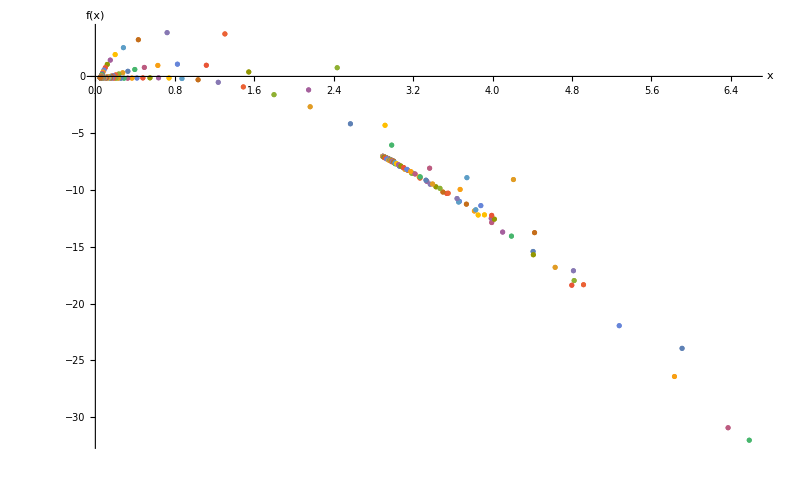

```mathematica
(*Show the plots on the same axes*)
(*When the curves cross f(x) = 0, an Einstein fixed point exists*)
Show[EinsteinPlots,PlotRange->Full,AxesLabel->{"x","f(x)"}]
```

#### 3-D Phase Space

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))+q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
(*β sets the sign of the square root in Y0*) 
trajFlat[Ωx0_,β_]=NDSolve[{deXt,deYt,deZt, X1[0]==x0/(1+x0),Y1[0]==β*y0/Sqrt[1+y0^2],Z1[0]==z0/(1+z0)}, {X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition (β √(0.0333333+(0.0333333 (1.-1. Ωx0))/Ωx0))/(√(1.03333+(0.0333333 (1.-1. Ωx0))/Ωx0)) is not a number or a rectangular array of numbers.

```mathematica
(*Solve for different initial conditions*)
```

```mathematica
sol[1]=trajFlat[0.6889,1]
sol[2]=trajFlat[0.1,1]
sol[3]=trajFlat[0.95,1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[4]=trajFlat[0.6889,-1]
sol[5]=trajFlat[0.1,-1]
sol[6]=trajFlat[0.95,-1]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Plot each trajectory*)
```

```mathematica
PhaseSpaceXYZFlat[1]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[1],{t,-6,100},PlotStyle -> {{Darker[Blue], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500,PlotRange->All];
```

```mathematica
PhaseSpaceXYZFlat[2]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[2],{t,-6,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpaceXYZFlat[3]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[3],{t,-10,100},PlotStyle -> {{Magenta, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpaceXYZFlat[4]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[4],{t,-100,6},PlotStyle -> {{Darker[Blue], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpaceXYZFlat[5]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[5],{t,-100,6},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpaceXYZFlat[6]=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[6],{t,-100,10},PlotStyle -> {{Magenta, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
PhaseSpaceXYZFlat=Table[PhaseSpaceXYZFlat[i],{i,1,6}];
```

```mathematica
(*Define the equation for the Flat Friedmann Separatrix (FFS)*)
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
(*Plot the FFS*)
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
(*The region above this surface is accelerating, and below is decelerating*)
AccnXYZ=ContourPlot3D[-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{X,0,1},{Y,-1,1},{Z,0,1},Mesh->None,ContourStyle->{Red,Opacity[0.2]}];
```

```mathematica
(*Plot the de Sitter line going through the two spiral fixed points*)
dSLine=ParametricPlot3D[{FP[6][[1]],Y,FP[6][[3]]},{X,0,1},{Y,-1,1},PlotPoints->100,PlotStyle->{{Black,Thickness[0.01]}}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinPointsFlat=ListPointPlot3D[{EinsteinPointFlatSol1i,EinsteinPointFlatSol1ii,EinsteinPointFlatSol2i,EinsteinPointFlatSol2ii},PlotStyle->Black];
```

```mathematica
(*Show the trajectories, the fixed points, the FFS and the boundary between accelerating and decelerating regions together*)
Show[PhaseSpaceXYZFlat,FFSPlus,FFSMinus,AccnXYZ,FPShowXYZ,CompactFPShow,EinsteinPointLineXYZ,EinsteinPointsFlat,PlotRange->{{0,1},{-1,1},{0,1}},AxesLabel->{MaTeX["X",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["Z",FontSize->20]},Ticks->{{0.0,0.5,1.0},{-1.0,-0.5,0.0,0.5,1.0},{0.0,0.5,1.0}},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400}]
```

-Graphics3D-

#### 2-D Z - X Projection

```mathematica
(*Plot the trajectories define above on the Z-X plane*)
```

```mathematica
PhaseSpaceXZFlat[1]=ParametricPlot[Evaluate[{Z1[t],X1[t]}/.sol[1],{t,-100,100},PlotStyle -> {{Darker[Blue], Opacity[0.75]}}],AxesLabel->{"Z","X"},PlotPoints->500];
```

```mathematica
PhaseSpaceXZFlat[2]=ParametricPlot[Evaluate[{Z1[t],X1[t]}/.sol[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"Z","X"},PlotPoints->500];
```

```mathematica
PhaseSpaceXZFlat[3]=ParametricPlot[Evaluate[{Z1[t],X1[t]}/.sol[3], {t,-100,100},PlotStyle -> {{Magenta, Opacity[0.75]}}],AxesLabel->{"Z","X"},PlotPoints->500];
```

```mathematica
(*Put the plots of the trajectories into a table*)
PhaseSpaceXZFlat=Table[PhaseSpaceXZFlat[i],{i,1,3}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions on the Z-X plane*)
AccnXZ=ContourPlot[-(1/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))==0,{Z,0,1},{X,0,1},ContourStyle->{Red,Opacity[0.8]},PlotPoints->200];
```

```mathematica
(*Define the Einstein fixed points in the Z-X plane*)
EinsteinPointFlatZXSol1i=Flatten[{zTableSol1xℛ[[PositionNearestToZero1xℛ]]/(1+zTableSol1xℛ[[PositionNearestToZero1xℛ]]),xTableSol1xℛ[[PositionNearestToZero1xℛ]]/(1+xTableSol1xℛ[[PositionNearestToZero1xℛ]])}];
EinsteinPointFlatZXSol2i=Flatten[{zTableSol2xℛ[[PositionNearestToZero2xℛ]]/(1+zTableSol2xℛ[[PositionNearestToZero2xℛ]]),xTableSol2xℛ[[PositionNearestToZero2xℛ]]/(1+xTableSol2xℛ[[PositionNearestToZero2xℛ]])}];

EinsteinPointFlatZXSol1ii=Flatten[{zTableSol1[[PositionNearestToZero1]]/(1+zTableSol1[[PositionNearestToZero1]]),xTableSol1[[PositionNearestToZero1]]/(1+xTableSol1[[PositionNearestToZero1]])}]
EinsteinPointFlatZXSol2ii=Flatten[{zTableSol2[[PositionNearestToZero2]]/(1+zTableSol2[[PositionNearestToZero2]]),xTableSol2[[PositionNearestToZero2]]/(1+xTableSol2[[PositionNearestToZero2]])}]
```

{0.756992,0.633557}

{0.865835,0.723658}

```mathematica
EinsteinPointsZXFlat=ListPlot[{EinsteinPointFlatZXSol1i,EinsteinPointFlatZXSol1ii,EinsteinPointFlatZXSol2i,EinsteinPointFlatZXSol2ii},PlotStyle->Black];
```

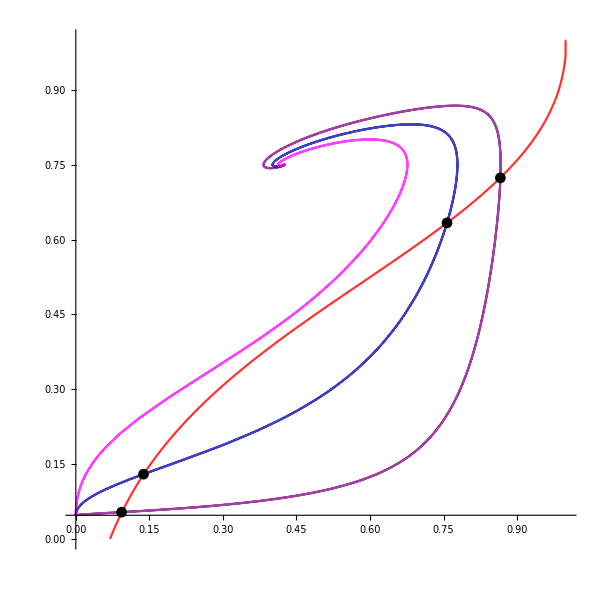

```mathematica
(*Show the trajectories and the boundary between accelerating and decelerating regions together*)
Show[PhaseSpaceXZFlat,AccnXZ,EinsteinPointsZXFlat,PlotRange->{{0,1},{0,1}},Axes->True,Frame->False,AxesLabel->{MaTeX["Z",FontSize->18],MaTeX["X",FontSize->18]},FrameTicks->{{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->18]},{Z,0.2Range[-1,5]}],None},{Table[{X,MaTeX[X,"DisplayStyle"->False,FontSize->18]},{X,0.2Range[-1,5]}],None}},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotRange->{{0,1},{0,1}},ImageSize->{600,600},PlotRangePadding->{0.08,0.08}]
```